R[T] = 100.252 (1+0.00378207 T)

R^2 = 1.

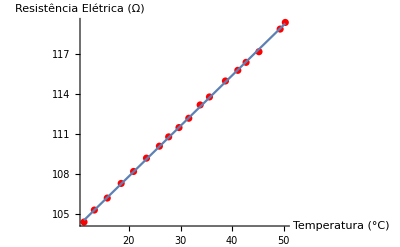

```mathematica
data={{11.3,104.4},{13.3,105.3},{15.8,106.2},{18.5,107.3},{20.9,108.2},{23.4,109.2},{25.9,110.1},{27.7,110.8},{29.7,111.5},{31.6,112.2},{33.8,113.2},{35.6,113.8},{38.7,115},{41.1,115.8},{42.7,116.4},{45.2,117.2},{49.3,118.9},{50.3,119.4}};

model=NonlinearModelFit[data, R0(1+α T), {R0, α}, {T}];
Print[R[T], " = ",Normal[model]]
Print[R^2, " = ", model["RSquared"]]

tf=Show[
ListPlot[data, PlotStyle->Red],
Plot[model[T],{T,Max[data[[All, 1]]], Min[data[[All, 1]]]}],
AxesLabel->{"Temperatura (°C)", "Resistência Elétrica (Ω)"}
];
Show[tf, ImageSize->Full]
Export[NotebookDirectory[]<>"Images/Temperatura/ResistenceTransferFunction.pdf", tf];
```

V[T] = -7.66095+0.0807481 T

R^2 = 0.999955

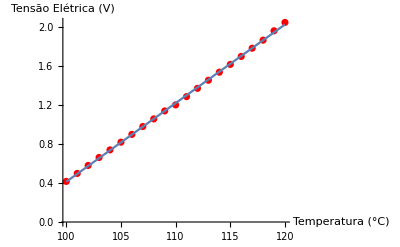

```mathematica
data={{100,0.417},{101,0.499},{102,0.581},{103,0.663},{104,0.741},{105,0.82},{106,0.9},{107,0.981},{108,1.059},{109,1.141},{110,1.203},{111,1.288},{112,1.373},{113,1.456},{114,1.539},{115,1.619},{116,1.701},{117,1.785},{118,1.868},{119,1.964},{120,2.05}};

model=NonlinearModelFit[data, V0+β T, {V0, β}, {T}];
Print[V[T], " = ",Normal[model]]
Print[R^2, " = ", model["RSquared"]]

tf=Show[
ListPlot[data, PlotStyle->Red],
Plot[model[T],{T,Max[data[[All, 1]]], Min[data[[All, 1]]]}],
AxesLabel->{"Temperatura (°C)", "Tensão Elétrica (V)"}
];
Show[tf, ImageSize->Full]
Export[NotebookDirectory[]<>"Images/Temperatura/ConditionatedTransferFunction.pdf", tf];
```

```mathematica
Export[NotebookFileName[]<>".pdf", EvaluationNotebook[]];
```